```mathematica
1
```

1

```mathematica
Integrate[E^(-Abs[x+y]/u)*(1/w-Abs[x]/w^2),{x,-w,w},Assumptions->Element[w,Reals]&&Element[u,Reals]&&u > 0 && w > 0&& Element[y,Reals]]
```

Piecewise[{{(ⅇ^(-w/u-y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w-y<0&&w>0&&y>0&&w+y>0}, {(ⅇ^(-w/u+y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w>0&&w-y>0&&y≤0&&w+y≤0}, {-(ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+2 ⅇ^(w/u+(2 y)/u) u-2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y))/w^2, y<0&&w>0&&w-y>0&&w+y>0}, {(ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^((2 y)/u) u+2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y))/w^2, w-y>0&&w>0&&y>0&&w+y>0}, {(ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+y/u) w-ⅇ^(w/u+y/u) y))/w^2, w-y==0&&w>0&&y>0&&w+y>0}, {-(ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+(2 y)/u) u-ⅇ^(w/u+y/u) w-ⅇ^(w/u+(2 y)/u) w-ⅇ^(w/u+y/u) y))/w^2, True}}]

```mathematica
f[y_,u_,w_] :=Piecewise[{{(ⅇ^(-w/u-y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w-y<0&&w>0&&y>0&&w+y>0}, {(ⅇ^(-w/u+y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w>0&&w-y>0&&y≤0&&w+y≤0}, {-1/w^2 ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+2 ⅇ^(w/u+(2 y)/u) u-2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y), y<0&&w>0&&w-y>0&&w+y>0}, {1/w^2 ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^((2 y)/u) u+2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y), w-y>0&&w>0&&y>0&&w+y>0}, {1/w^2 ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+y/u) w-ⅇ^(w/u+y/u) y), w-y==0&&w>0&&y>0&&w+y>0}, {-1/w^2 ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+(2 y)/u) u-ⅇ^(w/u+y/u) w-ⅇ^(w/u+(2 y)/u) w-ⅇ^(w/u+y/u) y), True}}]
```

```mathematica
Integrate[E^(-Abs[x+y]/u)*(1/w-Abs[x]/w^2),{x,-w,w},Assumptions->Element[w,Reals]&&Element[u,Reals]&&u > 0 && w > 0&& Element[y,Reals]&&w==1&&u==10]
```

Piecewise[{{10 (10-20 ⅇ^(1/10)+10 ⅇ^(1/5)) ⅇ^(-1/10-y/10), w==1&&y≥1}, {10 (10-20 ⅇ^(1/10)+10 ⅇ^(1/5)) ⅇ^(-1/10+y/10), w==1&&y≤-1}, {-10 ⅇ^(-1/10-y/10) (-10-2 ⅇ^(1/10+y/10)+20 ⅇ^(1/10+y/5)-10 ⅇ^(y/5)-2 ⅇ^(1/10+y/10) y), w==1&&-1<y<0}, {10 ⅇ^(-1/10-y/10) (10-9 ⅇ^(1/10+y/10)-9 ⅇ^(1/10+y/5)+10 ⅇ^(y/5)+ⅇ^(1/10+y/10) y), w==1&&y==0}, {-10 ⅇ^(-1/10-y/10) (-10+20 ⅇ^(1/10)-2 ⅇ^(1/10+y/10)-10 ⅇ^(y/5)+2 ⅇ^(1/10+y/10) y), True}}]

```mathematica
f[1,1,10]
```

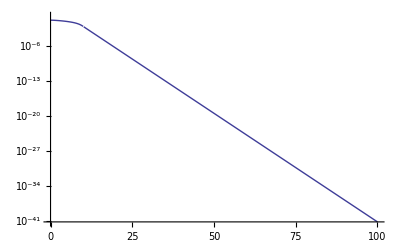

```mathematica
LogPlot[f[x,1,10],{x,0,100}]
```

```mathematica
FullSimplify[Piecewise[{{(ⅇ^(-w/u-y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w-y<0&&w>0&&y>0&&w+y>0}, {(ⅇ^(-w/u+y/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w>0&&w-y>0&&y≤0&&w+y≤0}, {-1/w^2 ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+2 ⅇ^(w/u+(2 y)/u) u-2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y), y<0&&w>0&&w-y>0&&w+y>0}, {1/w^2 ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^((2 y)/u) u+2 ⅇ^(w/u+y/u) w-2 ⅇ^(w/u+y/u) y), w-y>0&&w>0&&y>0&&w+y>0}, {1/w^2 ⅇ^(-w/u-y/u) u (u-2 ⅇ^(w/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+y/u) w-ⅇ^(w/u+y/u) y), w-y==0&&w>0&&y>0&&w+y>0}, {-1/w^2 ⅇ^(-w/u-y/u) u (-u-ⅇ^((2 y)/u) u+ⅇ^(w/u+y/u) u+ⅇ^(w/u+(2 y)/u) u-ⅇ^(w/u+y/u) w-ⅇ^(w/u+(2 y)/u) w-ⅇ^(w/u+y/u) y), True}}]]
```

Piecewise[{{(ⅇ^(-(w+y)/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w>0&&w<y}, {(ⅇ^((-w+y)/u) (-1+ⅇ^(w/u))^2 u^2)/w^2, w>0&&w+y≤0}, {(ⅇ^(-(w+y)/u) u ((1+ⅇ^((2 y)/u) (1-2 ⅇ^(w/u))) u+2 ⅇ^((w+y)/u) (w+y)))/w^2, y<0&&w+y>0}, {(ⅇ^(-(w+y)/u) u ((1-2 ⅇ^(w/u)+ⅇ^((2 y)/u)) u+2 ⅇ^((w+y)/u) (w-y)))/w^2, y>0&&y<w}, {(ⅇ^(-(2 y)/u) (-1+ⅇ^(y/u))^2 u^2)/y^2, w>0&&y>0&&w==y}, {(ⅇ^(-(w+y)/u) u ((1+ⅇ^((2 y)/u)) u+ⅇ^((w+y)/u) (-u+w+ⅇ^(y/u) (-u+w)+y)))/w^2, True}}]